# Задача о кратчайшей надстроке (Shortest superstring problEm)

## Решение задачи с помощью жадного алгоритма

## Работу выполнила Матвеева В., студентка гр. ПМ-2001

## Цель и задачи курсовой работы

### Цель:

решение задачи о кратчайшей надстроке с использованием жадного алгоритма

### Задачи:

реализация жадного алгоритма для решения задачи о кратчайшей надстроке;

визуализация решения на графе перекрытий;

сведение поставленной задачи к задаче о коммивояжере (TSP).

2

## Постановка задачи

Дан непустой набор строк S = {s_1,...,s_n}. Необходимо найти кратчайшую строку, содержащую все строки из исходного набора.

Некоторые области практического применения задачи:

секвенирование ДНК;

хранение и сжатие данных.

-Graphics-                          -Graphics-

3

## Термины, необходимые для понимания задачи

В строке s_i любая подстрока s_[1,j] является префиксом s_i.По аналогии, любая подстрока s_[j,|s_i|] называется суффиксом строки s_i.

Перекрытие 2-х строк s, t - самая длинной строка y, такая что  s = xy и 
t = yz для некоторых непустых x, z, причем x ≠ z.

Слияние 2-х строк s, t -  объединение этих двух строк с учетом их перекрытия.

4

## Методика жадного алгоритма при решении задачи о кратчайшей надстроке

На каждом шаге из S выбираются две строки s_i, s_j с наибольшим перекрытием ov(s_i, s_j) и заменяются их слиянием m(s_i, s_j). Алгоритм прекращает работу, когда остается только одна строка, и, очевидно, эта строка содержит все строки из исходного набора.

5

## Реализация жадного алгоритма на WL

Наибольшее перекрытие – это самая длинная строка, которая является суффиксом одной строки и префиксом другой.

```mathematica
Примеры функции нахождения длины максимального перекрытия:
```

```mathematica
maxOverlapLength["abc","tvp"]
```

0

```mathematica
maxOverlapLength["abbbbcccc","cccjjj"]
```

3

### Примеры работы основной функции:

```mathematica
solveSSP[{"ABA","ABB","AAA","AAB"}]
```

ABAAABB

```mathematica
solveSSP[{"ng_lon","_long_","a_long","long_l","ong_ti","ong_lo","long_t","g_long","g_time"}]
```

a_long_long_time

```mathematica
checkResult[%,{"ng_lon","_long_","a_long","long_l","ong_ti","ong_lo","long_t","g_long","g_time"}]
```

True

```mathematica
6
```

## Визуализация решений на графе перекрытий: создание графа

Каждому набору строк можно поставить в соответствие полный взвешенный ориентированный граф перекрытий G_o(S)=(V,E,w), где, V={s_1,…,s_n},E={(s_i,s_j):∀ s_i,s_j∈V,i≠j} , а w - весовая функция, сопоставляющая каждым 2-м вершинам длину их общего перекрытия.

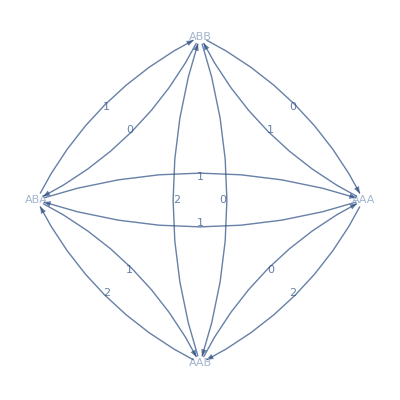

```mathematica
createGraph[{"ABA","ABB","AAA","AAB"}]
```

```mathematica
7
```

## Визуализация решений на графе перекрытий: получение пути, соответствующего решению задачи с помощью жадного алгоритма

Каждому решению задачи о кратчайшей надстроке можно сопоставить путь с максимальным итоговым перекрытием.

```mathematica
getPath["ABAAABB",{"ABA","ABB","AAA","AAB"}]
```

{ABA->AAA1,AAA->AAB2,AAB->ABB2}

```mathematica
8
```

## Визуализация решений на графе перекрытий: отображение пути на графе

```mathematica
highlightAnimate["ABAAABB",{"ABA","ABB","AAA","AAB"}]
```

```mathematica
highlightAnimate["a_long_long_",{"ng_lon","_long_","a_long","long_l","ong_lo","g_long"}]
```

```mathematica
9
```

## Сведение задачи о кратчайшей надстроке к другим перестановочным задачам

Задача поиска гамильтонова пути (Hamiltonian Path Problem) состоит в нахождении оптимального гамильтонова пути в соответствии с его весом.

Аналогично имеют место задачи максимизации и минимизации гамильтонова цикла, которые также известны как задачи коммивояжера (Min-Travelling Salesman Problem и Max-TSP).

```mathematica
10
```

## Сведение задачи о кратчайшей надстроке к другим перестановочным задачам

Оптимальное решение для набора S может быть получено путем нахождения максимального гамильтонова пути на G_o(S) = (V, E, w).

Максимальный гамильтонов цикл на G’  содержит максимальный гамильтонов путь на G_o(S), который, в свою очередь, соответствует кратчайшей настроке набора S.

```mathematica
11
```

## Результаты

В ходе работы :

была разобрана методика и идея жадного алгоритма при решении задачи о кратчайшей надстроке;

был реализован жадный алгоритм для решения задачи о кратчайшей надстроке и функции, необходимые для работы алгоритма;

была рассмотрена возможность решения поставленной задачи на графах и реализована визуализация решений на графе перекрытий;

была выявлена связь между поставленной задачей и задачами коммивояжера и поиска оптимального гамильтонова пути.

```mathematica
12
```

## Инициализация

### Основная функция

```mathematica
solveSSP[originalS_List]:=Module[
{s=originalS,maxOvLap=0,curOvLap,p1,p2},
p1=s⟦1⟧;If[Length[s]>1,p2=s⟦2⟧,Nothing];
While[ 
Length[s]≠1,
(*с помощью 2х циклов ищем наибольший оверлэп(просматривая все строки и их оверлэпы попарно)*)
Do[
Do[
If[s⟦i⟧≠s⟦j⟧,
curOvLap=maxOverlapLength[s⟦i⟧,s⟦j⟧];
If[curOvLap≥maxOvLap,maxOvLap=curOvLap;
p1=s⟦i⟧;p2=s⟦j⟧]];
,{j,Length[s]}];
,{i,Length[s]}];
(*формируем итоговую кратчайшую надстроку, содержащую все*)
s=ReplaceAll[s,{p1->Nothing,p2->Nothing}];
AppendTo[s,StringJoin[p1,StringPart[p2,maxOvLap+1;;]]];
(*обнуляем макс. овэрлэп, чтобы не произошло зацикливания и программа сработала до конца*)
maxOvLap=0
];
s⟦1⟧(*после работы цикла в списке остается 1 строка - ее и возвращаем*)
]
```

### Функция, выдающая длину перекрытия

```mathematica
maxOverlapLength[s1_,s2_]:=Module[
{s1len=StringLength@s1,s2len = StringLength@s2,ov=0,i,j,suff,pref},
For[
i=s1len;j=1,i>0&&j≤s2len,i--;j++,
pref=StringPart[s2,1;;j];
suff=StringPart[s1,i;;];
If[
suff==pref,ov=j,Nothing
]
];
ov
]
```

### Функция построения графа перекрытий набору строк

```mathematica
createGraph[s_]:=DirectedGraph[
DeleteCases[Flatten[Table[s⟦i⟧->s⟦j⟧,{i,Length[s]},{j,Length[s]}]],Rule[x_,x_]],{EdgeLabels->{"EdgeWeight"},EdgeWeight->DeleteCases[Flatten[Table[s⟦i⟧->s⟦j⟧->maxOverlapLength[s⟦i⟧,s⟦j⟧],{i,Length[s]},{j,Length[s]}]],Rule[DirectedEdge[u_,u_],_]],VertexShapeFunction->{"Name"}}
]
```

### Функция, выдающая путь, соответствующий порядку объединения строк в жадном алгоритме

```mathematica
getPath[x_,list_]:=Module[
{res={},l,len=StringLength@x},
Do[
l=StringLength@j;
If[
(!MemberQ[res,j])&&l+i-1≤len&&StringJoin@StringPart[x,i;;l+i-1]==j,AppendTo[res,j]
],{i,len},{j,list}
];
Table[Labeled[res⟦i⟧->res⟦i+1⟧,maxOverlapLength[res⟦i⟧,res⟦i+1⟧]],{i,Length@res-1}]
]
```

### Функция отображения пути на графе перекрытий

```mathematica
highlightAnimate[res_,s_]:=Module[
{g=createGraph[s]},
Animate[
HighlightGraph[g,{getPath[res,s]⟦1;;n⟧,PathGraph[getPath[res,s]⟦1;;n⟧]},GraphHighlightStyle->"Thick"],
{n,0,Length[getPath[res,s]],1},DefaultDuration->5]
]
```

### Функция, проверяющая результат работы жадного алгоритма на правильность

```mathematica
checkResult[x_String,list_List]:=StringContainsQ[x,list]
```

### Функция, выдающая кратчайшую надстроку и граф

```mathematica
solveSSP2[originalS_List]:=Module[
{s=originalS,maxOvLap=0,curOvLap,p1,p2,res={},last,path,ress,g},
g=createGraph[s];
p1=s⟦1⟧;If[Length[s]>1,p2=s⟦2⟧,Nothing];
While[ 
Length[s]≠1,
(*с помощью 2х циклов ищем наибольший оверлэп(просматривая все строки и их оверлэпы попарно)*)
Do[
Do[
If[s⟦i⟧≠s⟦j⟧,
curOvLap=maxOverlapLength[s⟦i⟧,s⟦j⟧];
If[curOvLap≥maxOvLap,maxOvLap=curOvLap;
p1=s⟦i⟧;p2=s⟦j⟧]];
,{j,Length[s]}];
,{i,Length[s]}];
AppendTo[res,{p1,p2}];
(*формируем итоговую кратчайшую надстроку, содержащую все*)
s=ReplaceAll[s,{p1->Nothing,p2->Nothing}];
AppendTo[s,StringJoin[p1,StringPart[p2,maxOvLap+1;;]]];
(*обнуляем макс. овэрлэп, чтобы не произошло зацикливания и программа сработала до конца*)
maxOvLap=0
];
{s⟦1⟧(*после работы цикла в списке остается 1 строка - ее и возвращаем*),highlightAnimate[s⟦1⟧,originalS]}
]
```

### Последняя функция

```mathematica
$Line=0;
```

```mathematica
13
```